# Superimposed Kerr Metric in Kerr-Schild coordinates ergosphere plot

## Import metric

```mathematica
Needs["MaTeX`"];
```

```mathematica
ClearAll[llgSKS,uugSKS];
Import["~/llgsks.mx"];
Import["~/uugsks.mx"];

Ω=Sqrt[(M1+M2)/b^3];
```

## Plot definitions

```mathematica
ClearAll[M1,M2,a1,a2,b]
M1=1/2;
M2=1/2;
a1=95/100*M1;
a2=95/100*M2;
b=3;
```

## Trajectory and radial distance

```mathematica
ClearAll[s];
s[bhIdx_,t_]:={(-1)^(bhIdx+1)b/2 Cos[Ω*t],(-1)^(bhIdx+1)b/2 Sin[Ω*t],0};

ClearAll[r];
r[bhIdx_,t_,x_,y_,z_]:=({x,y,z}-s[bhIdx,t]);

ClearAll[R];
R[bhIdx_,t_,x_,y_,z_]:=√(r[bhIdx,t,x,y,z].r[bhIdx,t,x,y,z])
```

## Ergosphere plot

### Centers

```mathematica
ClearAll[centers]
centers[t_]:=ListPlot[
{s[1,t]⟦1;;2⟧,s[2,t]⟦1;;2⟧},

PlotMarkers->Style["+",Black,Large],

PlotLegends->False,
PlotRange->Full
];
```

### Singularities

```mathematica
ClearAll[singularities]
singularities[t_]:=RegionPlot[
{
R[1,t,x,y,0]<a1,
R[2,t,x,y,0]<a2
},

{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->20,

BoundaryStyle->Directive[Black,Thick],
PlotStyle->White,

PlotLegends->False,
PlotRange->Full
];
```

### Horizons

```mathematica
ClearAll[horizons];
horizons[t_]:=ContourPlot[
{
R[1,t,x,y,0]==2M1(M1+√(M1^2-a1^2)),
R[2,t,x,y,0]==2M2(M2+√(M2^2-a2^2))
},

{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->20,

ContourShading->None,
ContourStyle->Directive[Gray,Thick],

PlotLegends->False,
PlotRange->{Full,Full,{-1,1}}
];
```

### Ergo contour

```mathematica
ClearAll[ergoContour];
ergoContour[T_]:=Block[
{expr},

expr=(llgSKS⟦1,1⟧)//.{t->T,z->0};

ContourPlot[
expr==0,

{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->20,

(* Exclude interior lines of singularity *)
RegionFunction->Function[{x,y,f},R[1,T,x,y,0]>a1+1/10&&R[2,T,x,y,0]>a2+1/10],

ContourShading->None,
ContourStyle->Directive[Red,Thick],

PlotLegends->False,
PlotRange->{Full,Full,{-1,1}}
]
];
```

### Full

```mathematica
ClearAll[full];
full[t_]:=Block[
{style},

style={
FontFamily->"TeX Gyre Pagella",
FontSize->12
};

Show[
ergoContour[t],
horizons[t],
singularities[t],
centers[t],

BaseStyle->style,
LabelStyle->style,

FrameStyle->BlackFrame
]
];
```

### Animation

```mathematica
ClearAll[animation];
animation[t0_,tf_,nt_]:=Block[
{dt,times,frames},

dt=(tf-t0)/nt;
times=Table[t0+i*dt,{i,0,nt-1}];
frames=ParallelMap[full,times];

ListAnimate[frames]
];
```

### Plot

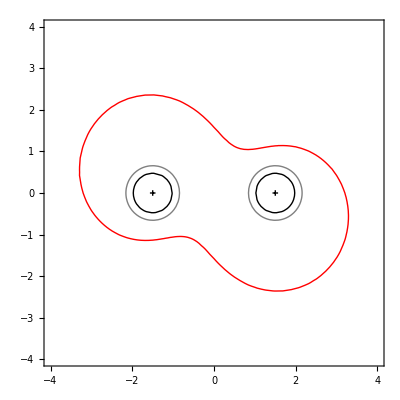

```mathematica
ClearAll[plot]
plot=full[0]
```

```mathematica
ClearAll[anim];
(*anim=animation[0,2π/Ω,60*5];*)
```

### Export

```mathematica
(*Export["sks_regions.pdf",plot]
Export["sks_regions.gif",anim]*)
```

sks_regions.pdf

## Ergosphere Value

```mathematica
N[llgSKS⟦1,1⟧//.{t->0,x->b/2+10/10,y->0,z->0}]
```

0.859134